# Associahedron Net: K4

## Computed Data

```mathematica
Clear[facets];

facets={{{1,2,3,4},{1,2,6,1},{1,6,2,1},{1,6,1,2},{1,4,1,4}},{{1,2,3,4},{1,2,6,1},{2,1,6,1},{2,1,3,4}},{{1,2,3,4},{1,4,1,4},{3,2,1,4},{3,1,2,4},{2,1,3,4}},{{2,1,3,4},{2,1,6,1},{4,1,4,1},{4,1,2,3},{3,1,2,4}},{{3,1,2,4},{3,2,1,4},{4,2,1,3},{4,1,2,3}},{{4,1,2,3},{4,1,4,1},{4,3,2,1},{4,3,1,2},{4,2,1,3}},{{1,4,1,4},{1,6,1,2},{4,3,1,2},{4,2,1,3},{3,2,1,4}},{{1,6,1,2},{1,6,2,1},{4,3,2,1},{4,3,1,2}},{{1,2,6,1},{1,6,2,1},{4,3,2,1},{4,1,4,1},{2,1,6,1}}};
```

## Transform 4D → 3D

```mathematica
Clear[transform];

transform[{x_,y_,z_,w_}]:=Block[
{m1},
m1=RowReduce[({{1/Sqrt[2], -1/(√6), -1/(2 √3), x}, {0, √(2/3), -1/(2 √3), y}, {0, 0, (√3)/2, z}, {-1/Sqrt[2], -1/(√6), -1/(2 √3), w-10}})];
Return[{
m1[[1]][[4]],
m1[[2]][[4]],
m1[[3]][[4]]
}];
];

facetsTransformed=Table[Table[
transform[facets[[i]][[j]]],
{j,1,Length[facets[[i]]]}],
{i,1,Length[facets]}];
```

## Unfold Net 3D → 2D

`facetsTransformed` is an array of 2D faces. Each 2D face is an array of 3D points.

My goal is to take the each 2D face and flatten it’s points into the appropriate 2-dimensional shape. For a given face, this should be a matter of finding an orthonormal basis for the plane-2 that the face rests inside, and then expressing the vertices of the face in terms of that basis.

```mathematica
Clear[unfoldFacet,facetsUnfolded];

unfoldFacet[facet2_]:=Block[
{origin,facet2Linear,b1,b2,basis,unfoldVertex},

origin=facet2[[1]]; (* choose arbitrary origin in plan *)
facet2Linear=Table[facet2[[i]]-origin,{i,1,Length[facet2]}];

(* choose arbitrary orthonormal basis *)
basis=Orthogonalize[{
facet2Linear[[2]],
facet2Linear[[3]]
}];
b1=basis[[1]]; b2=basis[[2]];

(* unfold vertex into 2D, in terms of basis *)
unfoldVertex[{x_,y_,z_}]:=Block[
{m},
m=RowReduce[({{b1[[1]], b2[[1]], x}, {b1[[2]], b2[[2]], y}, {b1[[3]], b2[[3]], z}})];
Return[Normalize[{
m[[1]][[3]],
m[[2]][[3]]
}]];
];

(* unfold all vertices *)
Return[Map[unfoldVertex,facet2Linear]];
];

facetsUnfolded=Map[unfoldFacet,facetsTransformed];
```

## Render Hull

```mathematica
Graphics3D[Map[Polygon,facetsTransformed]];
Table[Graphics3D[Polygon[facetsTransformed[[i]]]],{i,1,Length[facetsTransformed]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Render Net

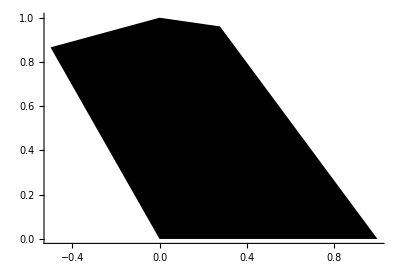
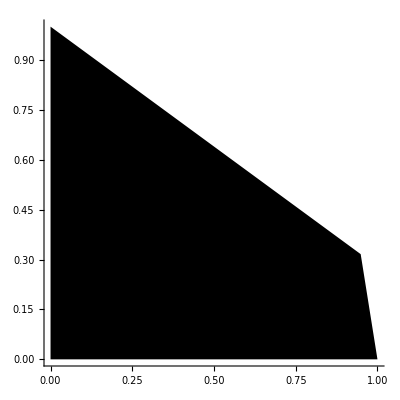
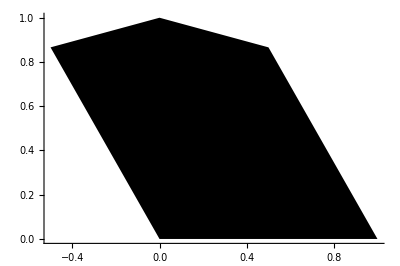
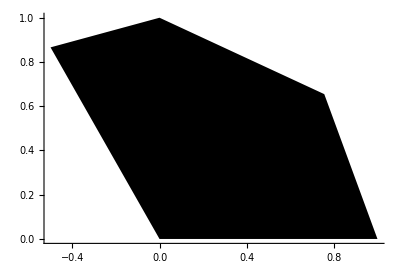
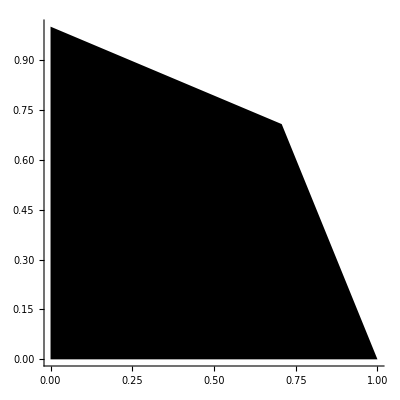
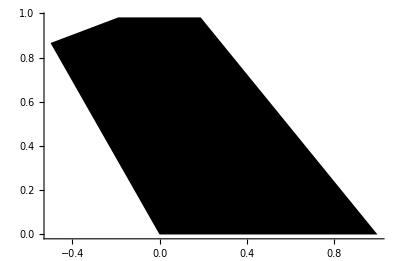
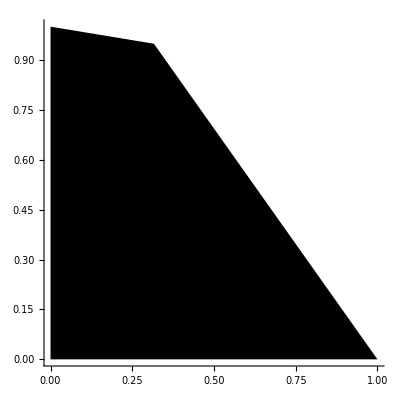
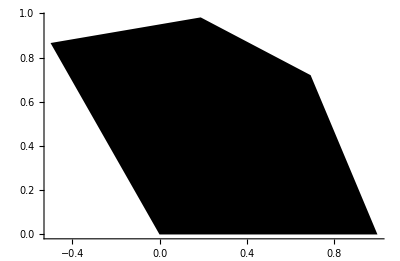
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[
Polygon[facetsUnfolded[[i]]],Axes->True
],{i,1,Length[facetsUnfolded]}]
```